```mathematica
f[x_]:= x + √x
```

```mathematica
k[x_]:= x^(-1/3)
```

```mathematica
carr = {1, 10, 0.1, 1, 1,1,1}
```

{1,10,0.1,1,1,1,1}

```mathematica
K1  = k
K2[i_]:= carr[i] k
K3[i_]:= carr[i] k
K4 = 1/k
K5 = k
K6 = k
K7 = k
```

```mathematica
-∫(x + √x)ⅆx
```

-(2 x^(3/2))/3-x^2/2

```mathematica
∫((-(2 x^(3/2))/3-x^2/2 + c1)/k[x])ⅆx
```

1/340 (255 c1 x^(4/3)-80 x^(17/6)-51 x^(10/3))

```mathematica
1/340 (255 c1 x^(4/3)-80 x^(17/6)-51 x^(10/3)) + с2 /.x-> 1.5
```

с2+1/340 (-449.391+437.853 c1)

```mathematica
1/340 (255 c1 x^(4/3)-80 x^(17/6)-51 x^(10/3)) + с2 /.x-> 2.5
```

с2+1/340 (-2154.49+865.221 c1)

```mathematica
Solve[{c2+1/340 (-449.39086059919043+437.85319777664944 c1)== 3,c2+1/340 (-2154.4935427777295+865.2206152896264 c1) == -3}, {c1,c2} ]
```

{{c1→-0.783629,c2→5.3309}}

```mathematica
1/340 (255 c1 x^(4/3)-80 x^(17/6)-51 x^(10/3)) + c2  /.{c1->-0.783628568996586,c2->5.330897457069074}
```

5.3309+1/340 (-199.825 x^(4/3)-80 x^(17/6)-51 x^(10/3))

```mathematica
f1[x_]:= 5.330897457069074+1/340 (-199.8252850941294 x^(4/3)-80 x^(17/6)-51 x^(10/3))
```

```mathematica
∫((-(2 x^(3/2))/3-x^2/2 + c1)/(10 k[x]))ⅆx
```

```mathematica
(255 c1 x^(4/3)-80 x^(17/6)-51 x^(10/3))/3400 + c2
```

```mathematica
(255 c1 x^(4/3)-80 x^(17/6)-51 x^(10/3))/3400 + c2/.x-> 1.5
```

(-449.391+437.853 c1)/3400+c2

```mathematica
(255 c1 x^(4/3)-80 x^(17/6)-51 x^(10/3))/3400 + c2/.x-> 2.5
```

(-2154.49+865.221 c1)/3400+c2

```mathematica
Solve[{(-449.39086059919043+437.85319777664944 c1)/3400+c2== 3,(-2154.4935427777295+865.2206152896264 c1)/3400+c2 == -3}, {c1,c2} ]
```

{{c1→-43.7443,c2→8.76558}}

```mathematica
(255 c1 x^(4/3)-80 x^(17/6)-51 x^(10/3))/3400 + c2 /.{{c1->-43.74432058160774,c2->8.76558279759501}}
```

{8.76558+(-11154.8 x^(4/3)-80 x^(17/6)-51 x^(10/3))/3400}

```mathematica
f2[x_]:=8.76558279759501+(-11154.801748309974 x^(4/3)-80 x^(17/6)-51 x^(10/3))/3400
```

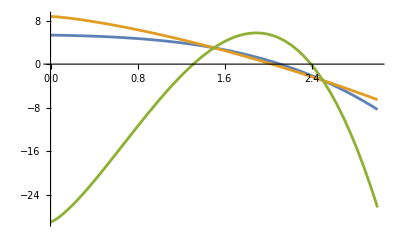

```mathematica
Plot[{5.330897457069074+1/340 (-199.8252850941294 x^(4/3)-80 x^(17/6)-51 x^(10/3)), 8.76558279759501+(-11154.801748309974 x^(4/3)-80 x^(17/6)-51 x^(10/3))/3400, -29.015955948190253-5. x^(4/3) (-5.268660948396789+0.47058823529411764 x^(3/2)+0.3 x^2)}, {x,0,3}]
```

```mathematica
∫((-(2 x^(3/2))/3-x^2/2 + c1)/(0.1 k[x]))ⅆx
```

```mathematica
-5. x^(4/3) (-1.5 c1+0.47058823529411764 x^(3/2)+0.3 x^2) + c2
```

```mathematica
-5. x^(4/3) (-1.5 c1+0.47058823529411764 x^(3/2)+0.3 x^2) + c2/.x-> 1.5
```

-8.58536 (1.53953-1.5 c1)+c2

```mathematica
-5. x^(4/3) (-1.5 c1+0.47058823529411764 x^(3/2)+0.3 x^2) + c2/.x-> 2.5
```

-16.9651 (3.73516-1.5 c1)+c2

```mathematica
Solve[{-8.585356819149988 (1.5395257915705334-1.5 c1)+c2== 3,-16.965110103718164 (3.7351633295108115-1.5 c1)+c2 == -3}, {c1,c2} ]
```

{{c1→3.51244,c2→-29.016}}

```mathematica
-5. x^(4/3) (-1.5 c1+0.47058823529411764 x^(3/2)+0.3 x^2) + c2 /.{c1->3.5124406322645263,c2->-29.015955948190253}
```

-29.016-5. x^(4/3) (-5.26866+0.470588 x^(3/2)+0.3 x^2)

```mathematica
f3[x_]:=-29.015955948190253-5. x^(4/3) (-5.268660948396789+0.47058823529411764 x^(3/2)+0.3 x^2)
```

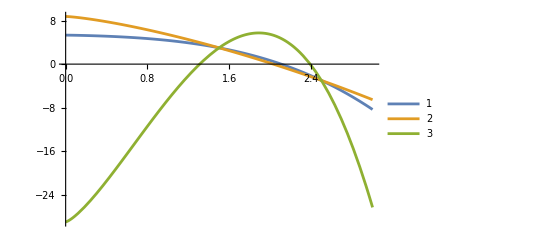

```mathematica
Plot[{f1[x], f2[x],f3[x]},{x,0,3}, PlotLegends->Automatic]
```

```mathematica
∫((-(2 x^(3/2))/3-x^2/2 + c1)k[x])ⅆx
```

1/208 (312 c1 x^(2/3)-64 x^(13/6)-39 x^(8/3))

```mathematica
1/208 (312 c1 x^(2/3)-64 x^(13/6)-39 x^(8/3)) + c2/.x-> 1.5
```

1/208 (-269.053+408.836 c1)+c2

```mathematica
1/208 (312 c1 x^(2/3)-64 x^(13/6)-39 x^(8/3)) + c2/.x-> 2.5
```

1/208 (-914.989+574.709 c1)+c2

```mathematica
Solve[{1/208 (-269.05252859736277+408.8356574965878 c1)+c2== 3,1/208 (-914.9885591970822+574.7089137879003 c1)+c2 == -3}, {c1,c2} ]
```

{{c1→-3.62966,c2→11.4278}}

```mathematica
1/208 (312 c1 x^(2/3)-64 x^(13/6)-39 x^(8/3)) + c2 /.{c1->-3.6296626886187995,c2->11.427827213411838}
```

11.4278+1/208 (-1132.45 x^(2/3)-64 x^(13/6)-39 x^(8/3))

```mathematica
f4[x_]:=11.427827213411838+1/208 (-1132.4547588490655 x^(2/3)-64 x^(13/6)-39 x^(8/3))
```

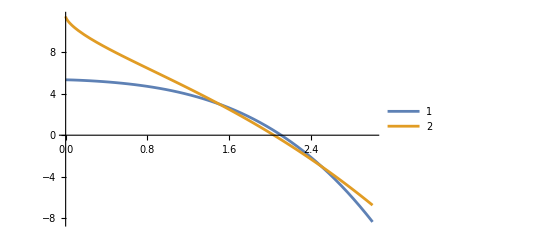

```mathematica
Plot[{f1[x],f4[x]},{x,0,3}, PlotLegends->Automatic]
```

```mathematica
1/340 (255 c1 x^(4/3)-80 x^(17/6)-51 x^(10/3)) +c2 /.x-> 1.5
```

1/340 (-449.391+437.853 c1)+c2

```mathematica
1/340 (255 c1 x^(4/3)-80 x^(17/6)-51 x^(10/3)) +c2 /.x-> 2.5
```

1/340 (-2154.49+865.221 c1)+c2

```mathematica
Solve[{1/340 (-449.39086059919043+437.85319777664944 c1)+c2== -3,1/340 (-2154.4935427777295+865.2206152896264 c1)+c2 == -3}, {c1,c2} ]
```

{{c1→3.98978,c2→-6.81632}}

```mathematica
1/340 (255 c1 x^(4/3)-80 x^(17/6)-51 x^(10/3)) +c2 /.{c1->3.9897816546268743,c2->-6.816317045028817}
```

-6.81632+1/340 (1017.39 x^(4/3)-80 x^(17/6)-51 x^(10/3))

```mathematica
f5[x_]:= -6.816317045028817+1/340 (1017.3943219298529 x^(4/3)-80 x^(17/6)-51 x^(10/3))
```

```mathematica
Solve[{1/340 (-449.39086059919043+437.85319777664944 c1)+c2== 3,1/340 (-2154.4935427777295+865.2206152896264 c1)+c2 == 3}, {c1,c2} ]
```

{{c1→3.98978,c2→-0.816317}}

```mathematica
1/340 (255 c1 x^(4/3)-80 x^(17/6)-51 x^(10/3)) +c2 /.{c1->3.9897816546268743,c2->-0.8163170450288177}
```

-0.816317+1/340 (1017.39 x^(4/3)-80 x^(17/6)-51 x^(10/3))

```mathematica
f6[x_]:= -0.8163170450288177+1/340 (1017.3943219298529 x^(4/3)-80 x^(17/6)-51 x^(10/3))
```

```mathematica
Solve[{1/340 (-449.39086059919043+437.85319777664944 c1)+c2== -3,1/340 (-2154.4935427777295+865.2206152896264 c1)+c2 == 3}, {c1,c2} ]
```

{{c1→8.76319,c2→-12.9635}}

```mathematica
1/340 (255 c1 x^(4/3)-80 x^(17/6)-51 x^(10/3)) +c2 /.{c1->8.763191878250336,c2->-12.963531547126708}
```

-12.9635+1/340 (2234.61 x^(4/3)-80 x^(17/6)-51 x^(10/3))

```mathematica
f7[x_]:=-12.963531547126708+1/340 (2234.6139289538355 x^(4/3)-80 x^(17/6)-51 x^(10/3))
```

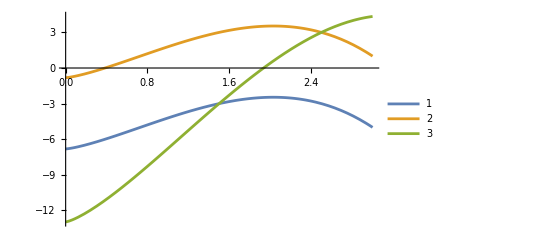

```mathematica
Plot[{f5[x],f6[x],f7[x]},{x,0,3}, PlotLegends->Automatic]
```